Pablo Chehade
Fecha de inicio: 2021/11/09
Última actualización: 2021/11/18

```mathematica
ClearAll["Global`*"]
(*Parámetros del problema:*)
Nmalla =5;
J = 1;
mu = 1;
kb = 1;

(*Si considero condiciones de borde no periódicas:
1.Cambiar el cociente de densidad de energía
2. cambiar índices en la construcción de malla0 para que sean nulos los elementos de los bordes.*)
```

```mathematica
(*Defino función pos() que se encarga de la periodicidad de la malla:*)
pos[k_]:=If[Mod[k,Nmalla]≠0,Mod[k,Nmalla],Nmalla];

DeltaE[malla_,x_,y_,flip_]:=Module[{deltaE},
(*Cálculo de/\E:;
Calcula la energía de interacción del elemento (i,j) con sus vecinos;
Si flip=false,calcula sin darlo vuelta;
Si flip=true,calcula dándolo vuelta;*)
deltaE = N[-J malla⟦x,y⟧ malla⟦pos[x+1],y⟧ (*arriba*)
-J malla⟦x,y⟧ malla⟦pos[x-1],y⟧(*abajo*)
-J malla⟦x,y⟧ malla⟦x,pos[y+1]⟧(*derecha*)
-J malla⟦x,y⟧ malla⟦x,pos[y-1]⟧(*izquierda*)];
If[flip==True,deltaE = -2*deltaE];
deltaE
];
Etot[malla_]:=Module[{etot},
etot = 0.;
Do[Do[
etot=etot+DeltaE[malla,i,j,False];
,{i,1,Nmalla}],{j,1,Nmalla}];
etot*0.5
]
(*Calculo la magnetización*)
Magnetizacion[malla_]:=Module[{mag},
mag = 0;
Do[Do[
mag=mag+ mu malla⟦i,j⟧;
,{i,1,Nmalla}],{j,1,Nmalla}];
mag
]
(*Factor de Boltzman*)
pBoltz[deltaE_, T_]:=N[E^(-deltaE/(kb T))];
```

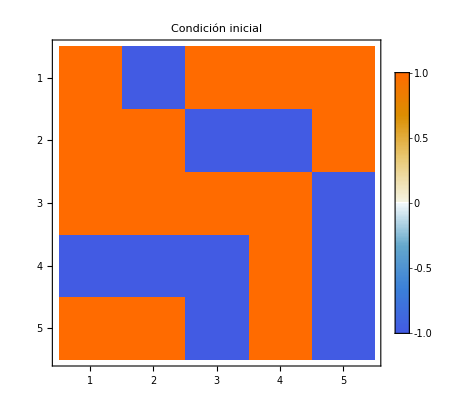

```mathematica
(*1. Genero una malla PERIÓDICA de tamaño Nmalla*Nmalla. Aleatoriamente asigno los estados 1 y -1. 1 indica spin up y -1, spin down.*)
malla0 = ConstantArray[0,{Nmalla,Nmalla}];
(*Condición inicial aleatoria:*)
Do[Do[
malla0⟦i,j⟧= RandomInteger[]*2-1;
,{i,1,Nmalla}],{j,1,Nmalla}];
MatrixPlot[malla0, PlotLabel->"Condición inicial", PlotLegends->True]
```

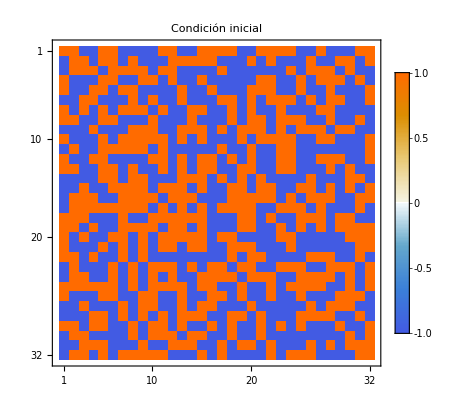
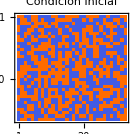

```mathematica
(*Defino el paso metrópolis*)
Metropolis[malla_, T_]:=Module[{mallatemp,xran,yran,deltaE, w, p},
mallatemp=malla;
(*4. Lazo de 1 a Nmalla x Nmalla*)
Do[
(*a) Me paro en (i,j) al azar*)
xran = RandomInteger[{1,Nmalla}];
yran = RandomInteger[{1,Nmalla}];
(*Print["k: ", k, " - xran: ", xran, " - yran: ", yran];*)
(*b) Calculo /\E correspondiente a flipear el sitio elegido*)
deltaE = DeltaE[malla,xran,yran,True];
p =pBoltz[deltaE, T];
w = RandomReal[];
If[w<=p,mallatemp⟦xran,yran⟧=-malla⟦xran,yran⟧ (*flipeo*);];
(*If[deltaE<0,
(*i.  Si /\E < 0, flipeo*)
mallatemp⟦xran,yran⟧=-malla⟦xran,yran⟧(*flipeo*),
(*ii.  Si /\E > 0, calculo el factor de Boltzmann p y sorteo uniformemente la variable w entre 0 y 1*)
w = RandomReal[]; (*w random entre 0 y 1*)
(*j. Si w > p, rechazo el flip;
jj. Si w <= p, acepto el flip, es decir, intercambio el valor del spin en la malla (multiplico por -1).;*)
If[w≤pBoltz[deltaE],
mallatemp⟦xran,yran⟧=-malla⟦xran,yran⟧ (*flipeo*)]
]*)
,{k,1,Nmalla^2}];
mallatemp
];
(*
malla=Metropolis[malla0];
MatrixPlot[malla]
malla=Metropolis[malla];
MatrixPlot[malla]
malla=Metropolis[malla];
MatrixPlot[malla]
malla=Metropolis[malla];
MatrixPlot[malla]
malla=Metropolis[malla];
MatrixPlot[malla]*)


Evolution[mallaInicial_,tmax_, T_]:=Module[{Energy, Mag, malla, EnergyDensity, MagDensity},
malla = mallaInicial;
(*2. Calculo la energía y la magnetización*)
Energy = ConstantArray[0,tmax];Mag = ConstantArray[0,tmax];
Energy⟦1⟧ = Etot[malla]; Mag⟦1⟧=Magnetizacion[malla];
(*3. Lazo temporal de 1 a tmax*)
Do[
malla = Metropolis[malla, T];
(*Actualizo Energía y magnetización.*)
Energy⟦t⟧ = Etot[malla]; Mag⟦t⟧=Magnetizacion[malla];
(*If[Mod[t,4]==0, Print[MatrixPlot[malla]]];*)
,{t,2,tmax}];
EnergyDensity = N[Energy/(Nmalla)^2];
MagDensity = N[Mag/(Nmalla)^2];
(*Para imprimir el resultado final:*)
(*Print[MatrixPlot[malla,  PlotLabel->"Estado final luego de t = " <> ToString[tmax] <> " - T = " <> ToString[T], PlotLegends->True]];*)
{EnergyDensity, MagDensity}
]
```

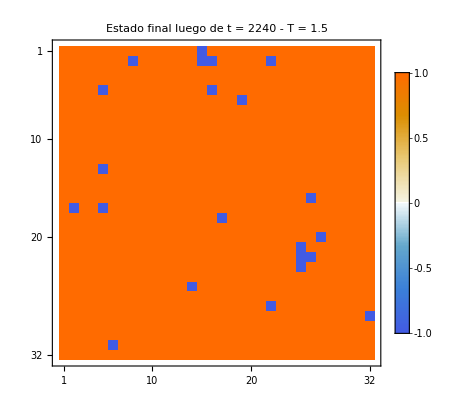

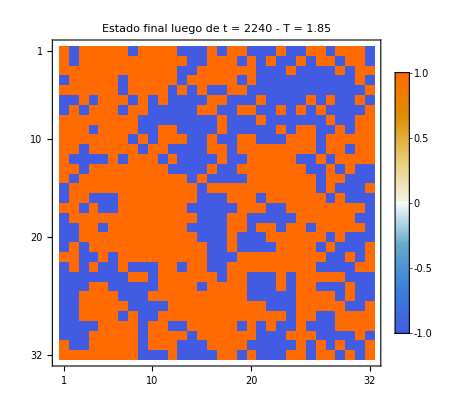

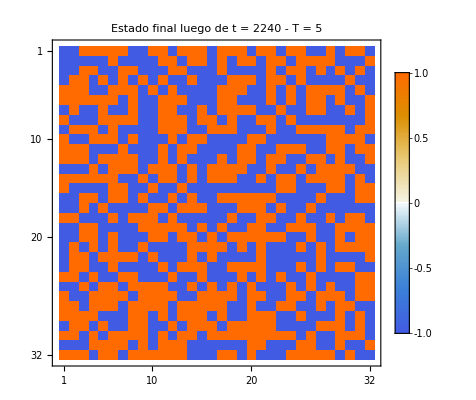

```mathematica
(*Evolución de la densidad de Energía y la Magnetización en el tiempo para T = 1.5, 2.35 y 5*)
tmax = 70*Nmalla;

T = 1.5;
{EnergyDensity1, MagDensity1}=Evolution[malla0,tmax, T];

T = 1.85;
{EnergyDensity2, MagDensity2}=Evolution[malla0,tmax, T];

T = 5;
{EnergyDensity3, MagDensity3}=Evolution[malla0,tmax, T];
```

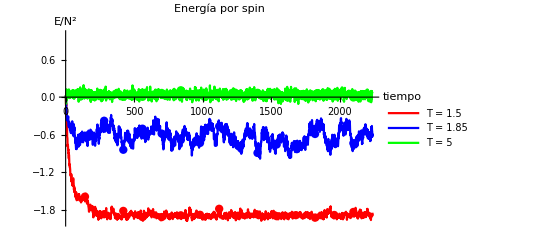

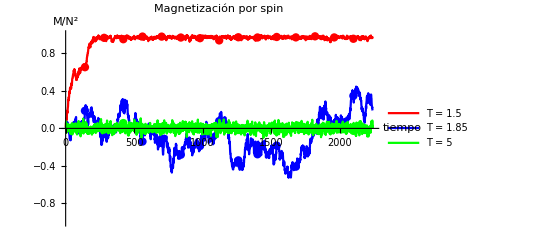

```mathematica
(*Gráficos de densidades de energía y magnetización en función del tiempo: *)

graphE1=ListPlot[Transpose[{Range[tmax], EnergyDensity1}], PlotLabel->"Energía por spin", Mesh->True, Joined->True, PlotRange->{All,{-2,1}}, PlotStyle->Red,PlotLegends->{"T = 1.5"}];
graphM1=ListPlot[Transpose[{Range[tmax], MagDensity1}], PlotLabel->"Magnetización por spin", Mesh->True, Joined->True, PlotRange->{All,{-1,1}}, PlotStyle->Red,PlotLegends->{"T = 1.5"}];
graphE2=ListPlot[Transpose[{Range[tmax], EnergyDensity2}], PlotLabel->"Energía por spin", Mesh->True, Joined->True, PlotRange->{All,{-2,1}},PlotStyle->Blue,PlotLegends->{"T = 1.85"}];
graphM2=ListPlot[Transpose[{Range[tmax], MagDensity2}], PlotLabel->"Magnetización por spin", Mesh->True, Joined->True, PlotRange->{All,{-1,1}}, PlotStyle->Blue,PlotLegends->{"T = 1.85"}];
graphE3=ListPlot[Transpose[{Range[tmax], EnergyDensity3}], PlotLabel->"Energía por spin", Mesh->True, Joined->True, PlotRange->{All,{-2,1}},PlotStyle->Green,PlotLegends->{"T = 5"}];
graphM3=ListPlot[Transpose[{Range[tmax], MagDensity3}], PlotLabel->"Magnetización por spin", Mesh->True, Joined->True, PlotRange->{All,{-1,1}}, PlotStyle->Green, PlotLegends->{"T = 5"}];
Show[{graphE1, graphE2, graphE3}, AxesLabel->{"tiempo","E/N^2"}]
Show[{graphM1, graphM2, graphM3}, AxesLabel->{"tiempo","M/N^2"}]
```

```mathematica
(*Función que para dada T calcula la magnetización para t=0,...,4*tmax.Luego,devuelve el valor medio y la desviación estandar de los valores entre 3 tmax y 4 tmax considerando que el sistema ya termalizó.;*)
Termalizacion[T_,tmax_]:=Module[{malla0,EnergyDensity, MagDensity},
malla0 = ConstantArray[0,{Nmalla,Nmalla}];
Do[Do[
malla0⟦i,j⟧= RandomInteger[]*2-1;
,{i,1,Nmalla}],{j,1,Nmalla}];
{EnergyDensity, MagDensity}=Evolution[malla0,4tmax, T];
{Mean[MagDensity⟦1tmax;;2tmax⟧], MeanDeviation[MagDensity⟦1tmax;;2tmax⟧],Mean[EnergyDensity⟦1tmax;;2tmax⟧], MeanDeviation[EnergyDensity⟦1tmax;;2tmax⟧]}
];

(*Función que para dada T calcula la magnetización de una serie de ensambles.Devuelve 2 listas:una de valores medios y otra de desviaciones estándar*)
Ensambles[T_,tmax_,Nensamble_]:=Module[{EnsambleMagMean, EnsambleMagDesv,EnsambleEnerMean, EnsambleEnerDesv},
EnsambleMagMean=ConstantArray[0,Nensamble];
EnsambleMagDesv=ConstantArray[0,Nensamble];
EnsambleEnerMean=ConstantArray[0,Nensamble];
EnsambleEnerDesv=ConstantArray[0,Nensamble];
Do[
{EnsambleMagMean⟦k⟧, EnsambleMagDesv⟦k⟧,EnsambleEnerMean⟦k⟧, EnsambleEnerDesv⟦k⟧} = Termalizacion[T, tmax]
,{k,1,Nensamble}];
{EnsambleMagMean, EnsambleMagDesv,EnsambleEnerMean, EnsambleEnerDesv}
]

(*
T = 1.5;
tmax = 10*Nmalla;
Nensamble = 10;
{EnsambleMean,EnsambleDesv} =Ensambles[T, tmax, Nensamble]
Temp = ConstantArray[T, Nensamble];
ListPlot[Transpose[{Temp,Abs[EnsambleMean]}], PlotRange->{All, {0,1}}]
*)
(*Función que realiza el diagrama de fases de magnetización vs T entre Tmin y Tmax con espaciado hT*)
DiagramaFases[Tmin_, Tmax_, hT_,tmax_, Nensamble_]:=Module[{Temperaturas,x,y,z,EnsambleMagMean,EnsambleMagDesv,EnsambleEnerMean, EnsambleEnerDesv,Temp},
Temperaturas = Range[Tmin, Tmax, hT];
x ={}; y = {}; z={};
Do[
{EnsambleMagMean,EnsambleMagDesv, EnsambleEnerMean, EnsambleEnerDesv} =Ensambles[Temperaturas⟦k⟧, tmax, Nensamble];
Temp = ConstantArray[Temperaturas⟦k⟧, Nensamble];
y = Join[y, EnsambleMagMean]; x = Join[x,Temp]; z = Join[z,EnsambleMagDesv];
Print["Progreso: ", N[100 k/Length[Temperaturas],2], "%"];
,{k,1,Length[Temperaturas]}];
Print[ListPlot[Transpose[{x,y}], PlotLabel->"Diagrama de fases", AxesLabel->{"T","M/N^2"}]];
{x,y,z}
]
```

Progreso: 6.3%

Progreso: 13.%

Progreso: 19.%

Progreso: 25.%

Progreso: 31.%

Progreso: 38.%

Progreso: 44.%

Progreso: 50.%

Progreso: 56.%

Progreso: 63.%

Progreso: 69.%

Progreso: 75.%

Progreso: 81.%

Progreso: 88.%

Progreso: 94.%

Progreso: 100.%

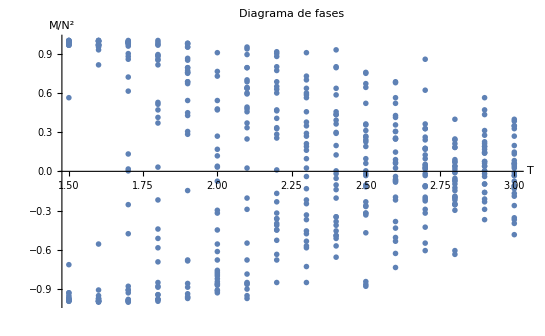

{{1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.7,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.8,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.},{0.562724,-0.949821,0.992832,-0.928315,-0.985663,0.985663,1.,1.,0.964158,-0.713262,0.964158,-0.971326,0.971326,-0.928315,0.985663,-0.978495,0.985663,1.,-0.964158,-0.978495,0.985663,0.964158,-0.985663,-0.985663,0.992832,-0.992832,-0.992832,-0.985663,0.985663,0.992832,-0.985663,1.,0.964158,0.949821,0.964158,-0.978495,-1.,0.928315,-0.971326,0.964158,1.,0.971326,-0.992832,1.,0.992832,0.81362,-0.90681,-0.992832,-0.971326,0.964158,-0.992832,0.992832,0.992832,-0.992832,-0.949821,-0.992832,0.956989,0.992832,0.971326,-0.555556,-0.978495,0.992832,0.00358423,0.956989,-1.,0.899642,-0.985663,-0.878136,0.971326,-0.90681,0.985663,0.978495,0.992832,0.856631,0.985663,-0.992832,0.0179211,0.978495,0.72043,-0.985663,0.132616,0.985663,1.,-0.90681,-0.476703,-0.928315,0.878136,-0.25448,0.612903,-0.992832,-0.44086,0.892473,0.985663,-0.218638,0.885305,-0.878136,1.,-0.584229,-0.691756,0.856631,-0.885305,0.469534,-0.849462,-0.978495,-0.978495,0.849462,-0.992832,0.369176,-0.512545,-0.942652,0.81362,0.971326,0.878136,-0.942652,0.526882,0.0322581,-0.978495,0.964158,0.512545,0.412186,0.770609,0.863799,0.949821,0.756272,0.978495,-0.935484,-0.971326,0.448029,0.684588,0.670251,0.971326,-0.856631,0.949821,-0.964158,0.978495,-0.956989,0.792115,0.426523,0.283154,-0.677419,0.304659,0.749104,0.756272,0.541219,-0.146953,0.849462,0.684588,-0.684588,0.792115,-0.885305,-0.612903,-0.820789,0.0322581,0.476703,-0.863799,-0.842294,-0.297491,0.0394265,0.763441,0.268817,0.727599,-0.928315,-0.555556,-0.799283,-0.0752688,-0.448029,0.11828,0.168459,-0.784946,-0.770609,-0.677419,0.469534,0.90681,-0.90681,-0.913978,-0.318996,-0.756272,0.541219,-0.856631,-0.870968,0.892473,0.698925,-0.949821,-0.856631,-0.971326,0.792115,-0.784946,0.684588,-0.677419,0.935484,-0.204301,0.0250896,0.333333,0.247312,0.792115,-0.548387,-0.899642,0.949821,0.369176,0.634409,0.591398,0.491039,0.455197,0.598566,0.634409,-0.290323,-0.863799,0.476703,-0.849462,0.641577,-0.634409,0.770609,0.648746,0.799283,-0.362007,-0.448029,0.899642,-0.849462,-0.412186,0.62724,0.469534,0.0107527,0.326165,0.598566,-0.232975,0.25448,-0.362007,-0.677419,0.283154,0.684588,-0.397849,-0.168459,0.462366,-0.526882,0.333333,0.405018,-0.318996,-0.448029,0.878136,0.913978,0.634409,0.21147,-0.476703,0.34767,-0.369176,0.189964,-0.727599,-0.849462,0.90681,-0.0394265,-0.132616,-0.333333,-0.53405,-0.247312,0.268817,-0.455197,-0.584229,0.562724,0.290323,0.0250896,0.0967742,-0.218638,-0.569892,0.584229,0.598566,0.376344,0.698925,0.727599,0.455197,0.16129,0.455197,-0.569892,0.390681,-0.34767,0.290323,0.433692,-0.204301,-0.103943,0.297491,0.799283,-0.491039,-0.383513,0.00358423,-0.0537634,0.197133,-0.412186,-0.455197,0.584229,0.792115,-0.139785,-0.0179211,0.125448,0.928315,0.362007,-0.34767,-0.655914,0.634409,-0.491039,-0.512545,0.433692,0.519713,-0.878136,0.362007,0.311828,0.0609319,-0.842294,0.756272,-0.232975,-0.318996,-0.268817,-0.318996,-0.469534,-0.333333,0.354839,0.240143,0.261649,-0.11828,-0.0179211,0.670251,-0.261649,0.268817,0.749104,0.0967742,-0.0322581,0.00358423,0.225806,0.641577,-0.863799,0.189964,-0.103943,0.677419,0.426523,-0.734767,0.0681004,-0.505376,-0.433692,0.412186,-0.0681004,0.562724,0.0250896,0.304659,-0.0824373,0.25448,-0.197133,-0.0752688,0.0896057,-0.0394265,0.304659,0.354839,0.684588,0.247312,0.247312,-0.383513,-0.0609319,-0.53405,0.0609319,-0.62724,0.146953,0.519713,-0.218638,-0.111111,0.175627,0.0322581,-0.11828,0.175627,0.620072,0.0250896,0.168459,0.240143,0.261649,-0.197133,0.326165,0.125448,-0.225806,0.0967742,-0.426523,0.0179211,-0.0179211,-0.290323,-0.111111,-0.318996,0.046595,0.326165,0.856631,-0.0322581,-0.21147,-0.605735,0.0537634,0.362007,-0.548387,-0.0681004,0.397849,-0.25448,0.0394265,-0.00358423,-0.125448,-0.204301,-0.189964,-0.0537634,-0.0967742,0.21147,0.247312,0.0179211,-0.197133,0.0752688,-0.605735,0.0681004,-0.0107527,0.240143,-0.0752688,0.182796,-0.25448,-0.218638,-0.634409,-0.247312,0.182796,0.0394265,-0.146953,0.0896057,-0.297491,-0.0967742,0.189964,0.311828,0.21147,0.225806,0.0752688,-0.290323,0.139785,0.139785,0.0609319,-0.0179211,0.562724,-0.16129,0.00358423,-0.16129,0.433692,-0.232975,0.0752688,0.168459,0.275986,-0.21147,0.469534,0.146953,0.0394265,-0.0967742,0.00358423,0.189964,-0.0394265,-0.369176,0.0394265,-0.111111,-0.111111,0.268817,-0.132616,0.197133,-0.0752688,-0.189964,-0.354839,-0.483871,0.383513,0.132616,0.0609319,-0.261649,-0.125448,-0.0322581,0.0394265,0.0250896,0.326165,0.0537634,-0.0322581,-0.168459,0.34767,0.34767,-0.0107527,-0.369176,0.0824373,0.146953,0.0609319,-0.397849,0.397849},{0.422245,0.0809342,0.0138744,0.120245,0.0268239,0.0268239,0.,0.,0.0601226,0.331137,0.0601226,0.0517979,0.049948,0.106371,0.0268239,0.0388484,0.0268239,0.,0.062435,0.0388484,0.0268239,0.0601226,0.0268239,0.0268239,0.0138744,0.0138744,0.0138744,0.0268239,0.0268239,0.0138744,0.0268239,0.,0.0601226,0.0776968,0.0601226,0.0388484,0.,0.110995,0.049948,0.0601226,0.,0.049948,0.0138744,0.,0.0138744,0.192392,0.126257,0.0138744,0.049948,0.062435,0.0138744,0.0138744,0.0138744,0.0138744,0.0874089,0.0138744,0.0693722,0.0138744,0.049948,0.55914,0.0388484,0.0138744,0.799168,0.0721471,0.,0.155394,0.0268239,0.149381,0.049948,0.138282,0.0268239,0.0388484,0.0138744,0.129495,0.0268239,0.0138744,0.661348,0.0402359,0.267777,0.0268239,0.607238,0.0268239,0.,0.13227,0.502255,0.110995,0.172968,0.291363,0.395884,0.0138744,0.512892,0.17343,0.0268239,0.864377,0.140594,0.141519,0.,0.504105,0.263152,0.203492,0.140594,0.474968,0.155394,0.0388484,0.0388484,0.18453,0.0138744,0.531853,0.422708,0.0850965,0.204417,0.0517979,0.165106,0.0850965,0.440282,0.812579,0.0388484,0.0601226,0.333911,0.487918,0.311712,0.149381,0.0874089,0.287201,0.0388484,0.0957336,0.049948,0.475893,0.349636,0.410683,0.049948,0.175743,0.0809342,0.0647474,0.0388484,0.0804717,0.174355,0.573939,0.684472,0.331599,0.402359,0.241415,0.285813,0.43242,0.777893,0.18453,0.320962,0.366285,0.187767,0.162793,0.309862,0.219679,0.372297,0.444907,0.193317,0.223841,0.385709,0.369985,0.235403,0.295988,0.326049,0.101746,0.430108,0.220141,0.319112,0.36906,0.709909,0.271014,0.208117,0.211816,0.259914,0.375535,0.120245,0.13227,0.116545,0.516592,0.232628,0.391259,0.175743,0.174818,0.145682,0.259452,0.0809342,0.166493,0.049948,0.295063,0.263614,0.302925,0.3094,0.0957336,0.751994,0.633599,0.458781,0.513354,0.187767,0.43982,0.129495,0.0841716,0.225691,0.457394,0.244653,0.414846,0.375997,0.273789,0.371372,0.388484,0.18453,0.397734,0.203954,0.310325,0.329287,0.24049,0.404209,0.258989,0.515204,0.483755,0.129495,0.165106,0.268702,0.260377,0.409758,0.433345,0.209966,0.18453,0.568852,0.372297,0.369985,0.245578,0.55359,0.179905,0.36166,0.700197,0.460631,0.479593,0.587814,0.356111,0.62065,0.475431,0.149381,0.110995,0.291363,0.460631,0.254365,0.232628,0.565152,0.502255,0.283039,0.194242,0.126257,0.523066,0.284426,0.344086,0.340386,0.721933,0.556365,0.462019,0.343161,0.37831,0.457394,0.561915,0.477281,0.606313,0.342699,0.302,0.325587,0.460169,0.326049,0.318187,0.538791,0.524916,0.381085,0.3168,0.288588,0.304313,0.353798,0.428258,0.360273,0.294138,0.373685,0.207192,0.279801,0.36721,0.447682,0.467569,0.320499,0.315875,0.409758,0.351948,0.241415,0.407908,0.362585,0.259452,0.110995,0.527691,0.456469,0.3057,0.332524,0.308475,0.396809,0.398196,0.581339,0.125795,0.44167,0.295988,0.327437,0.183143,0.216904,0.476356,0.36351,0.568389,0.260377,0.384322,0.286738,0.523991,0.284888,0.341774,0.451382,0.253902,0.318187,0.437045,0.330674,0.288126,0.303388,0.262689,0.268239,0.611863,0.367673,0.18453,0.353798,0.424095,0.218291,0.354261,0.290438,0.606313,0.258989,0.304313,0.400971,0.632212,0.308937,0.321424,0.406059,0.397271,0.229853,0.48468,0.462481,0.258527,0.508267,0.406059,0.495317,0.277951,0.321424,0.415308,0.349636,0.373685,0.353336,0.345011,0.289513,0.378772,0.406983,0.42687,0.673835,0.254827,0.282114,0.42317,0.410683,0.438895,0.513354,0.42132,0.454619,0.556827,0.742745,0.394959,0.332986,0.412071,0.24974,0.284888,0.219216,0.325587,0.362585,0.430108,0.446757,0.267314,0.237715,0.184992,0.568852,0.312175,0.371835,0.231703,0.293213,0.281651,0.566077,0.445369,0.301538,0.212279,0.319575,0.233553,0.360273,0.339461,0.388947,0.274714,0.433345,0.343624,0.24789,0.355648,0.378772,0.354261,0.505954,0.313562,0.440282,0.218291,0.556827,0.416233,0.398196,0.333449,0.300613,0.466181,0.270089,0.307088,0.410683,0.275639,0.418083,0.271939,0.370447,0.348711,0.661811,0.3094,0.259452,0.414846,0.30385,0.238178,0.313562,0.366285,0.330674,0.290438,0.255752,0.317262,0.382472,0.297375,0.256215,0.353336,0.342236,0.361198,0.335761,0.284426,0.418083,0.398196,0.363048,0.422708,0.292751,0.317725,0.258065,0.258065,0.320499,0.409296,0.232166,0.273326,0.348711,0.356111,0.274714,0.317725,0.284426,0.262227,0.322349,0.289976,0.511504,0.265002,0.369985,0.3094,0.403284,0.391722,0.267314,0.332986,0.388484,0.269164,0.354723,0.377385,0.471731,0.521679,0.25529,0.289976}}

Fiscom_TP06_ejercicio1_DiagramaDeFases.dat

```mathematica
(*Diagrama de fases*)
T = 1.5;
tmax = 10*Nmalla;
Nensamble = 30;
Tmin = 1.5; Tmax = 3.; hT = 0.1;
{x,y,z} = DiagramaFases[Tmin, Tmax, hT, tmax, Nensamble];

archivo = "Fiscom_TP06_ejercicio1_DiagramaDeFases.dat";
Export[archivo, ExportString[Transpose[{x,y,z}],"Table","FieldSeparators"->" ",Alignment->Left]]
```

```mathematica
(*para dada T,toma los valores medios y desviaciones estándar de la magnetización de un ensamble y calcula el valor medio y la dispersión. Devuelve 4 listas: el valor medio de la magnetización, la dispersión, la desviación estándar y el error calculado como la suma cuadrática de lso dos anteriores.*)
DiagramaFasesPro[Tmin_, Tmax_, hT_,tmax_, Nensamble_]:=Module[{Temperaturas,x,y,Temp, EnsambleMagMean, EnsambleMagDesv, EnsambleEnerMean, EnsambleEnerDesv, MagMean, MagDisp, MagDesv, MagError,EnerMean, EnerDisp, EnerDesv, EnerError},
Temperaturas = Range[Tmin, Tmax, hT];
MagMean = ConstantArray[0,Length[Temperaturas]];
MagDisp = ConstantArray[0,Length[Temperaturas]]; (*dispersión de los puntos - fórmula página 115 del apunte de Chule*)
MagDesv = ConstantArray[0,Length[Temperaturas]]; (*Suma cuadrática de los errores de cada punto que promedio*)
MagError= ConstantArray[0,Length[Temperaturas]];
EnerMean = ConstantArray[0,Length[Temperaturas]];
EnerDisp = ConstantArray[0,Length[Temperaturas]];
EnerDesv = ConstantArray[0,Length[Temperaturas]];
EnerError= ConstantArray[0,Length[Temperaturas]];

Do[
{EnsambleMagMean,EnsambleMagDesv, EnsambleEnerMean, EnsambleEnerDesv} =Ensambles[Temperaturas⟦k⟧, tmax, Nensamble];

MagMean⟦k⟧=Mean[Abs[EnsambleMagMean]];
MagDisp⟦k⟧ = MeanDeviation[Abs[EnsambleMagMean]];
Do[MagDesv⟦k⟧ = MagDesv⟦k⟧ + EnsambleMagDesv⟦j⟧^2,{j,1,Nensamble}];
MagDesv⟦k⟧ =(MagDesv⟦k⟧ ^0.5)/Nensamble;
(*Sumo cuadráticamente los errores dispersión y desviación*)
MagError⟦k⟧ = (MagDisp⟦k⟧^2 +MagDesv⟦k⟧^2)^0.5 ;

EnerMean⟦k⟧=Mean[Abs[EnsambleEnerMean]];
EnerDisp⟦k⟧ = MeanDeviation[Abs[EnsambleEnerMean]];
Do[EnerDesv⟦k⟧ = EnerDesv⟦k⟧ + EnsambleEnerDesv⟦j⟧^2,{j,1,Nensamble}];
EnerDesv⟦k⟧ =(EnerDesv⟦k⟧ ^0.5)/Nensamble;
(*Sumo cuadráticamente los errores dispersión y desviación*)
EnerError⟦k⟧ = (EnerDisp⟦k⟧^2 +EnerDesv⟦k⟧^2)^0.5 ;
Print["Progreso: ", N[100 k/Length[Temperaturas],2], "%"];
,{k,1,Length[Temperaturas]}];


{MagMean, MagDisp, MagDesv, MagError,EnerMean, EnerDisp, EnerDesv, EnerError}
]
```

```mathematica
(*Test de desviaciones estándar y dispersión*)
tmax = 50*Nmalla;
Nensamble = 40;
Tmin = 1.5; Tmax = 3.; hT = 0.03;


{MagMean, MagDisp, MagDesv, MagError,EnerMean, EnerDisp, EnerDesv, EnerError} =DiagramaFasesPro[Tmin, Tmax, hT, tmax, Nensamble];
Print["Magnetización: ", MagMean, "\nDispersión: ", MagDisp, "\nDesviación estándar: ", MagDesv, "\nError total: ", MagError]
archivo = "Fiscom_TP06_ejercicio1_DiagramaDeFasesPro.dat";
Export[archivo, ExportString[Transpose[{MagMean, MagDisp,MagDesv}],"Table","FieldSeparators"->" ",Alignment->Left]]
```

Progreso: 2.%

Progreso: 3.9%

Progreso: 5.9%

Progreso: 7.8%

Progreso: 9.8%

Progreso: 12.%

Progreso: 14.%

Progreso: 16.%

Progreso: 18.%

Progreso: 20.%

Progreso: 22.%

Progreso: 24.%

Progreso: 25.%

Progreso: 27.%

Progreso: 29.%

Progreso: 31.%

Progreso: 33.%

Progreso: 35.%

Progreso: 37.%

Progreso: 39.%

Progreso: 41.%

Progreso: 43.%

Progreso: 45.%

Progreso: 47.%

Progreso: 49.%

Progreso: 51.%

Progreso: 53.%

Progreso: 55.%

Progreso: 57.%

Progreso: 59.%

Progreso: 61.%

Progreso: 63.%

Progreso: 65.%

Progreso: 67.%

Progreso: 69.%

Progreso: 71.%

Progreso: 73.%

Progreso: 75.%

Progreso: 76.%

Progreso: 78.%

Progreso: 80.%

Progreso: 82.%

Progreso: 84.%

Progreso: 86.%

Progreso: 88.%

Progreso: 90.%

Progreso: 92.%

Progreso: 94.%

Progreso: 96.%

Progreso: 98.%

Progreso: 100.%

Magnetización: {0.954398,0.937251,0.936064,0.91008,0.83894,0.830247,0.825817,0.756876,0.628135,0.612199,0.586781,0.543275,0.461681,0.393116,0.34239,0.324948,0.250582,0.201219,0.187442,0.158558,0.165426,0.146717,0.14498,0.102821,0.109187,0.119968,0.118159,0.0942629,0.076749,0.0793705,0.0718167,0.0638725,0.0624701,0.0665498,0.0491952,0.055012,0.0515697,0.0543586,0.062247,0.048255,0.0426215,0.0489402,0.0509323,0.0411873,0.040008,0.0371155,0.038502,0.0388287,0.0328367,0.0346454,0.0350677}
Dispersión: {0.0296331,0.0486474,0.034247,0.070761,0.18032,0.155777,0.132805,0.188685,0.248716,0.247425,0.242572,0.241105,0.233188,0.209748,0.199853,0.184216,0.143522,0.112765,0.109976,0.112595,0.0921932,0.0927486,0.0648267,0.0646104,0.0897964,0.0702151,0.0618514,0.0517849,0.0529323,0.0438267,0.0372323,0.03571,0.0358725,0.0401578,0.0337163,0.0355108,0.0383777,0.0323068,0.0374215,0.0247139,0.0217892,0.0274924,0.031855,0.0231502,0.0222721,0.0241251,0.0306964,0.0216653,0.0165665,0.0233562,0.0221534}
Desviación estándar: {0.0204506,0.0249657,0.0188211,0.0307048,0.0487168,0.0457309,0.0443708,0.0555383,0.0707236,0.0699676,0.069233,0.0681945,0.0722131,0.0724416,0.0770126,0.0699479,0.075815,0.0747307,0.066897,0.0635417,0.059871,0.0609418,0.0553477,0.05653,0.053481,0.051085,0.0524905,0.0495173,0.0484384,0.0467896,0.0446134,0.0431847,0.0432422,0.0424169,0.0405932,0.0410817,0.0385491,0.0394045,0.0390797,0.0377034,0.0373159,0.0375926,0.0370493,0.0356765,0.0352436,0.0346308,0.0344605,0.0338858,0.0341475,0.0334685,0.0330888}
Error total: {0.0360048,0.0546796,0.039078,0.0771356,0.186785,0.162351,0.140021,0.196689,0.258576,0.257128,0.252259,0.250564,0.244113,0.221906,0.214178,0.197048,0.162316,0.135279,0.128724,0.129287,0.109928,0.110978,0.0852401,0.0858495,0.104516,0.0868323,0.0811224,0.0716494,0.0717503,0.0641097,0.0581085,0.0560367,0.0561847,0.058411,0.0527693,0.0543021,0.0543956,0.0509553,0.0541072,0.0450813,0.0432117,0.046573,0.0488609,0.0425293,0.0416912,0.0422056,0.0461497,0.0402198,0.037954,0.0408124,0.0398201}

Fiscom_TP06_ejercicio1_DiagramaDeFasesPro.dat

```mathematica
Range[1.5,3.,0.1]
```

{1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.}

```mathematica
(*Nensamble = 10, tmax = 10*Nmalla, Nmalla = 6*)
"Magnetización: "{0.9775045537340615,0.6302367941712202,0.29225865209471763,0.1174863387978142,0.06675774134790527,0.08060109289617486}"\nDispersión: "{0.010728597449908985,0.24371584699453544,0.15890710382513654,0.06265938069216757,0.03907103825136611,0.04326047358834243}"\nDesviación estándar: "{0.10695743503259536,0.5854043299843702,0.6971428289949527,0.670401177413978,0.5513023401399785,0.5907933898607277}"\nError total: "{0.10749416594398996,0.6341101194908604,0.715024189566464,0.6733230552021622,0.552685096844357,0.5923751328999366}
(*Nensamble = 100, tmax = 10*Nmalla, Nmalla = 6*)
"Magnetización: "{0.9669398907103824,0.6827868852459015,0.2026229508196721,0.08141165755919856,0.07419854280510019,0.05968123861566485}"\nDispersión: "{0.015415300546448095,0.20676684881602903,0.1319285974499089,0.058032058287796,0.047342076502732255,0.03656010928961749}"\nDesviación estándar: "{0.44017377487616755,2.169656328574007,2.634586610398828,2.1489635562643588,1.8778428956390147,1.6936070947839807}"\nError total: "{0.44044362134065734,2.179486433518353,2.6378877463830577,2.1497469818426254,1.8784395686072817,1.6940016626597225}
(*La desviación estándar aumenta enormemente*)
(*Nensamble = 100, tmax = 30*Nmalla, Nmalla = 6*)
"Magnetización: "{0.9666052793124617,0.6375107427869858,0.1553468385512584,0.062034990791896893,0.03879373848987109,0.03612645794966237}"\nDispersión: "{0.01180724370779636,0.2099043585021485,0.0897794966236955,0.038943707796193994,0.024831246163290365,0.019993861264579495}"\nDesviación estándar: "{0.48822088746379294,3.1999457663445168,3.1595002005103634,2.315087792816905,1.9361567434320008,1.754751982623769}"\nError total: "{0.4883636411117323,3.2068228431368633,3.160775517976408,2.3154153192951723,1.936315967481349,1.75486588519189}
(*La dispersión mejora, pero la desviación estandar no mejora mucho*)
```

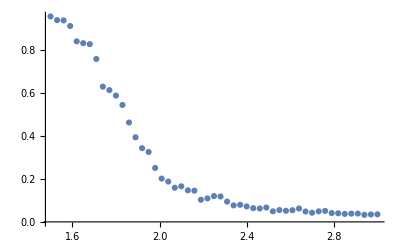

Temperatura de Curie:
Analítica: Tc =  2.269185
Computacional con <|m|>: Tc = {1.71}

```mathematica
(*Temperatura de Curie: la calculo como el máximo de la derivada d<|m|>/dT*)
(*Calculo la derivada aproximadamente usando la fórmula turbia de 4 términos del capítulo 1. Tenía la ventaja de que el error es orden h^4*)
(*HAY QUE EJECUTAR LA CELDA ANTERIOR*)
(*tmax = 10*Nmalla;
Nensamble = 10;
Tmin = 1.5; Tmax = 3.; hT = 0.1;
{MagMean, MagDisp, MagDesv, MagError,EnerMean, EnerDisp, EnerDesv, EnerError} =DiagramaFasesPro[Tmin, Tmax, hT, tmax, Nensamble];*)
MagMeanAbs = Abs[MagMean];
Temperaturas = Range[Tmin, Tmax, hT];

ListPlot[Transpose[{Temperaturas, MagMeanAbs}]]
DerivadaMag = ConstantArray[0,Length[Temperaturas]];

Do[
DerivadaMag⟦k⟧=1/(12 hT)(-MagMeanAbs⟦k+2⟧ + 8 MagMeanAbs⟦k+1⟧ - 8 MagMeanAbs⟦k-1⟧+ MagMeanAbs⟦k-2⟧),
{k,1+2,Length[Temperaturas]-2}];
(*Busco el mínimo (cambio negativo más grande de <|m|>) de la lista DerivadaMag*)
pos=Ordering[DerivadaMag,1];
(*max=Extract[DerivadaMag,pos];*) (*Valor en el máximo*)
Print["Temperatura de Curie:", "\nAnalítica: Tc =  2.269185", "\nComputacional con <|m|>: Tc = ", Temperaturas⟦pos⟧]
```

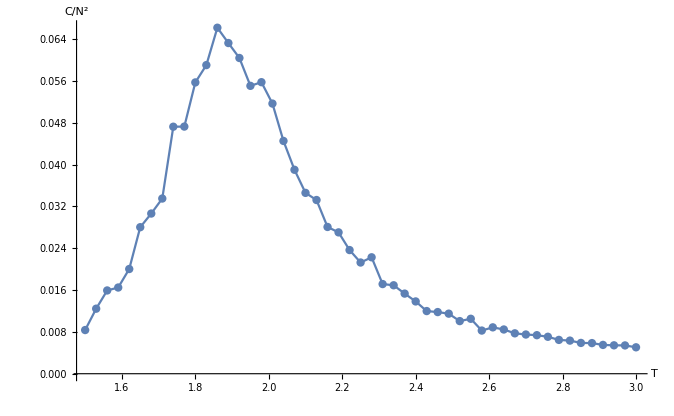

Temperatura de Curie:
Analítica: Tc =  2.269185
Computacional con C: Tc = {2.22}

```mathematica
(*Capacidad calorífica - hay que ejecutar la celda anterior antes*)
Temperaturas = Range[Tmin, Tmax, hT];
Cap = ConstantArray[0,Length[Temperaturas]];
Do[
Cap⟦k⟧=Nmalla^2*EnerDesv⟦k⟧^2/(kb (Temperaturas⟦k⟧)^2) (*EnerDesv está en unidades de energía/Nmalla^2, recordemos que Ener es densidad*)
,{k,1,Length[Temperaturas]}]
ListPlot[Transpose[{Temperaturas,Cap}], AxesLabel->{"T","C/N^2"}, Joined->True, Mesh->All]

(*En T = Tc, C diverge. Entonces calculemos Tc como T tal que Cv es máximo:*)
pos=Ordering[DerivadaMag,-1];
Print["Temperatura de Curie:", "\nAnalítica: Tc =  2.269185", "\nComputacional con C: Tc = ", Temperaturas⟦pos⟧]
```